```mathematica
(* Defining the coefficients for Taylor *)
truncExp[n_,x_]:=Series[Exp[n x],{x,0,n}]//Normal;
zerosTaylor[n_]:=Solve[truncExp[n,x]==0,x];
coeffsTaylor[n_]:=-1/x/.zerosTaylor[n];
```

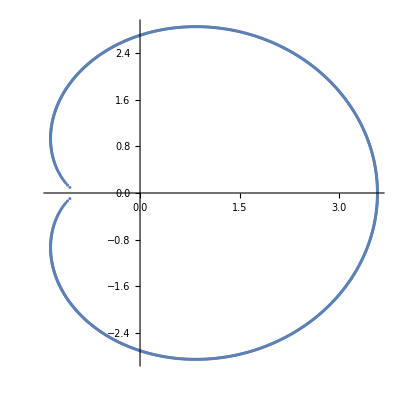

```mathematica
(* They take this shape for a large number of points *)
ListPlot[(Tooltip[{Re[#1],Im[#1]}]&)/@(coeffsTaylor[1000]//N),AspectRatio->1]
```

```mathematica
(* Different types of approximations to exp(i x): Chebyshev (blue), Taylor (green), Chabyshev fitted to exp(x) (organge) *)
Manipulate[LogPlot[{Abs[Exp[I x]+BesselJ[0,10]-2 Sum[(-I)^k BesselJ[k,10]ChebyshevT[k,-x/10],{k,0,n}]],
Abs[Exp[I x]+BesselJ[0,10I]-2 Sum[(-I)^k BesselJ[k,10I]ChebyshevT[k,I x/10],{k,0,n}]],Abs[Exp[I x]-Sum[(I x)^k/k!,{k,0,n}]]},{x,-10,10},PlotRange->All],{{n,30},1,100,1}]
```

```mathematica
(* Some explicit coefficients for cutoffs 2, 4, and 8 *)
N[coeffsTaylor[2],17]//MatrixForm
N[coeffsTaylor[4],17]//MatrixForm
N[coeffsTaylor[8],17]//MatrixForm
```

(1.-1. ⅈ
1.+1. ⅈ)

(1.8294933739891903-0.9404019519941707 ⅈ
1.8294933739891903+0.9404019519941707 ⅈ
0.1705066260108097-1.5785318126884535 ⅈ
0.1705066260108097+1.5785318126884535 ⅈ)

(2.5115385528762511-0.6852625793459637 ⅈ
2.5115385528762511+0.6852625793459637 ⅈ
1.681001528801266-1.7481130845728929 ⅈ
1.681001528801266+1.7481130845728929 ⅈ
0.4249750401763088-2.0321227226190966 ⅈ
0.4249750401763088+2.0321227226190966 ⅈ
-0.617515121853826-1.4284655522676216 ⅈ
-0.617515121853826+1.4284655522676216 ⅈ)

```mathematica
(* Defining the coefficients for Chebyshev *)
truncCheb[a_,n_,x_]:=N[-BesselJ[0,a]+2 Sum[(-I)^k BesselJ[k,a]ChebyshevT[k,x],{k,0,n}],70]//Simplify;
zerosCheb[a_,n_]:=Solve[truncCheb[a,n,I x]==0,x];
coeffsCheb[a_,n_]:=-n/a/x/.zerosCheb[a,n];
```

```mathematica
(* Calculate and store coefficients for plotting(this might take a while)*)
c4=coeffs[4];
c10=coeffs[10];
c52=coeffs[52];
c88=coeffs[88];
c100=coeffs[100];
c304=coeffs[304]//N;
cheb100C152=coeffsCheb[100,152];
cheb100IC152=coeffsCheb[100I,152];
```

```mathematica
(* Produce the plots of zeros *)
ComplexListPlot[{-52/c52,-304/c304,-152/cheb100C152,-152/cheb100IC152},AspectRatio->1,PlotRange->All,PlotLegends->Placed[{"z^(52)","z^(304)","z_c^(152)(100i)","z_c^(152)(100)"},{{1,.85},{0.8,0.5}}],AxesLabel->{"Re(z)","Im(z)"}]
```

-Graphics-

```mathematica
(* ...and coefficients *)
ComplexListPlot[{c4,c10,c52,c304},AspectRatio->1,AxesLabel->{"Re(γ)","Im(γ)"},PlotLegends->Placed[{"γ^(4)","γ^(10)","γ^(52)","γ^(304)"},{{1,.85},{0.8,0.5}}]]
```

-Graphics-